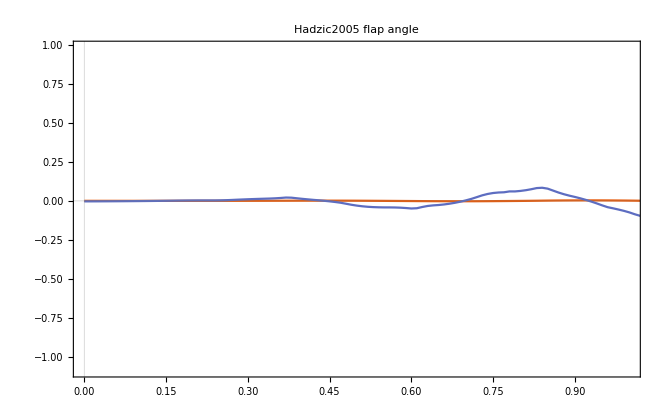

```mathematica
ClearAll["Global`*"];
data=Import[NotebookDirectory[]<>"./SPHERIC_TestCase12/Flap.dat","Data"];
data={#1,#2/180*Pi}&@@@data;
velocity=Import[NotebookDirectory[]<>"../Hadzic2005Flap_check.dat","Data"];
velocity=velocity[[1;;,{1,6}]];
ListPlot[{data[[2;;]],velocity},PlotLabel->"Hadzic2005 flap angle",PlotTheme->"Scientific",Joined->{True,True},PlotRange->{{0,1.},All}]
```

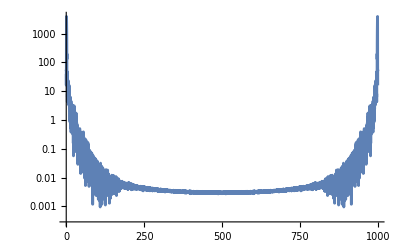

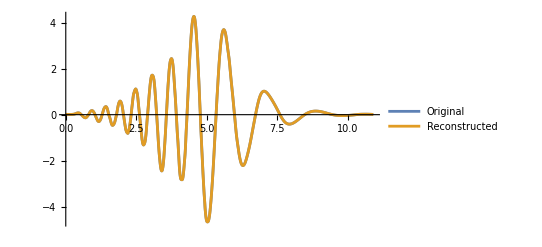

```mathematica
times=data[[2;;,1]];
angles=data[[2;;,2]];

(*Perform Fourier Transform*)
ft=Fourier[angles,FourierParameters->{1,-1}];

(*Compute the frequencies*)
freqs=Range[0,Length[angles]-1]/(Last[times]-First[times]);

(*Only keep the first half of the spectrum*)
half=Ceiling[Length[ft]];
ft=ft[[1;;half]];
freqs=freqs[[1;;half]];

(*Plot the magnitude of the Fourier Transform*)
ListLogPlot[Transpose[{freqs,Abs[ft]}],Joined->True,PlotRange->All]

(*Perform Inverse Fourier Transform*)
reconstructedAngles=InverseFourier[ft,FourierParameters->{1,-1}];

(*Pad the reconstructed data with zeroes to match original data length*)
reconstructedAngles=PadRight[reconstructedAngles,Length[angles]];

(*Compare the original data with the reconstructed data,plotting against time*)
ListLinePlot[{Transpose[{times,angles}],Transpose[{times,Re[reconstructedAngles]}]},PlotLegends->{"Original","Reconstructed"}]
```